DeepLaetitia: Deep Reinforcement Learning that makes you smile

Dendek Adam

Bernard Etienne

AGH University of Science and Technology, Krakow Poland

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: 
The aim of this project is to train Deep Reinforcement Learning agent to bring a smile to your face.

SUMMARY OF WORK: 
The first part of the project was to train Deep Convoluted Neural Network to predict one of five (happy, neutral, sad, angry, surprised) facial emotions.
The input to this classifier is taken directly from the user’s camera.  
Then, taken it’s prediction as an input, reinforcement learning agent was trained to makes you smile.  the tunable emoticon was used.

RESULTS AND FUTURE  WORK: 
The first phase of the project was to implement the facial emotion detector.
At the beginning of my study I trained classical Machine Learning models, such as Supported Vector Machine, Random Forest, k Nearest Neighborhood. This models was used as a performance baseline for further studies based on Deep Convoluted Neural Networks. 
My analyse shows that, model contained two hidden convoluted layers, is the best classifier. Selected model archived performance of 91%, measured as area under Receiver Operating Characteristic curve, in happiness recognition.  
Then, based on chosen model prediction, the policy to find the funniest emoticon was obtained. To do it the Monte Carlo based searching method was applied. 
From the future perspective the Q-Learning approach will be implemented. A starting point of the further studies will be Monte Carlo tuned policy from the previous step.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

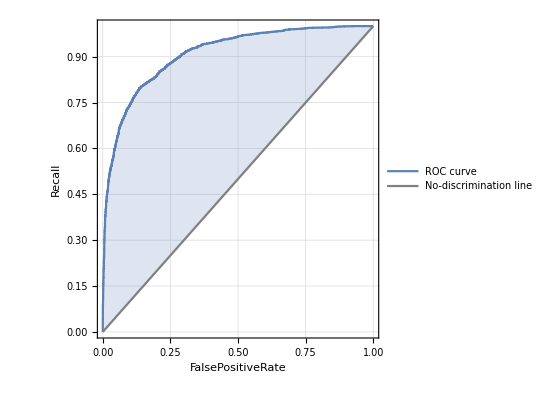
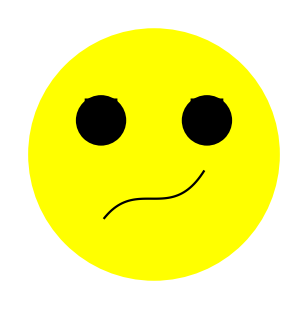
"happy"→-Graphics- -Graphics-

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

## Phase One: facial emotion detector:

As mentioned before, the best facial emotion detector is Deep Convolution Neural Network.  
Above cell presents architecture (upper right plot) of selected network and training progress related plots.

The model was trained using O(20k) 50x50 pixel grayscale facial expression labeled images.  Below cell shows a couple of training examples.  Each of this pictures belong to one of following class: 
happy, neutral, sad, angry, surprised.

Classifier performance measurement was performed on O(7k) testing images. 
At first  I present confusion matrix which is a specific table layout that allows visualization of the performance of an algorithm. Each column of the matrix represents the instances in a predicted class while each row represents the instances in an actual class. The name stems from the fact that it makes it easy to see if the system is confusing two classes (i.e. commonly mislabelling one as another).

Another widely used classifier metrics is area under Receiver Operating Characteristic curve, which can be understood as an equal to the probability that a classifier will rank a randomly chosen positive instance higher than a randomly chosen negative one.

The obtained results for particular classes:

<|”happy”→0.909475, ”neutral”→0.82957,”sad”→0.796471,”angry”→ 0.81805,”surprise”→0.934574|>}

What is worth to mention that the classifier evaluation time is very small. It  can be run in online mode.

Code

All source code is stored in the Github repository:

https://github.com/adendek/DeepLaetitia

Written Content / Lesson Plans

Conclusions in Detail

All Visualizations

Data Sources Links/References

The data used to train the  model was taken from Kaggle platform:
https://www.kaggle.com/c/challenges-in-representation-learning-facial-expression-recognition-challenge

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

Deep Reinforcement Learning

Machine Learning

Computer Vision

Deep Learning

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```